SIRCm model: equilibrium and stability analysis

1. Quick context:
This is a modified SIRC epidemiological model where the cross-immunity erosion rates are driven by infection prevalence rather than being fixed constants

In the original SIRC:  δ (R→C rate) and γ (C→S rate) are constants.

In our modification (SIRCm):
• δ = δ′ · β S I
• γ = γ′ · β S I

Where β  is the contact rate, S is the proportion of susceptible people and I is the proportion of infected/infective people. All together, β S I represents the infection incidence.

The motivation is that mutations arise proportionally to the number of active infections, since  each replication event is an opportunity for mutation. 

The constants δ′ and γ′  are expressed in this notebook as δp and γp 

2. Parameter Restrictions:

All parameters are positive by biological definition:
• μ > 0 : birth/death rate (demographic turnover)
• β > 0 : contact rate
• α > 0 : recovery rate. (its inverse is the average time spent in the I compartment) 
• σ ∈ (0, 1) : cross-immunity factor (0 = full immunity, 1 = none)

All compartments are population fractions:
• S, I, R, C ≥ 0 and S + I + R + C = 1

• In particular, at the endemic equilibrium: 0 < I < 1

3. What we need:
In the original SIRC model, the basic reproduction number is R0 = β / (μ + α), which represents the average number of secondary infections produced by a single infected individual in a fully susceptible population.

The system has two equilibria: a disease-free equilibrium (DFE) at (S, I, R, C) = (1, 0, 0, 0), and an endemic equilibrium where the disease persists at a positive level I > 0. A bifurcation occurs at R0 = 1: when R0 < 1, the DFE exists and it is stable (every small outbreak dies out). When R0 > 1, the endemic equilibrium emerges and is stable (the disease persists). 

We have already verified that the DFE of the SIRCm model is the same to that of the original SIRC, with the same stability threshold (R0 < 1). This is expected because when I = 0, all infection-driven terms vanish and the modification has no effect.

The question now is what happens when R0 > 1. Does a unique endemic equilibrium exist? Is it stable? How does the infection-driven feedback change the bifurcation compared to the original SIRC?

I need help with the endemic equilibrium. We want to... 

1. Derive the polynomial whose roots give the endemic equilibrium values of I (the infected fraction of the population) 

2. Determine whether a biologically meaningful root (0 < I < 1) exists and is unique when R0 > 1

3. Analyze stability of the endemic equilibrium via the characteristic polynomial of the Jacobian

(note: in this notebook we are using “II” as I and “CC” as C since both “I” and “C” are reserved in mathematica)


4. the SIRCm model:

```mathematica
ClearAll["Global`*"]

dS=μ*(1-S)-β*S*II+(γp*β*S*II)*CC;
dI=β*S*II+σ*β*CC*II-(μ+α)*II;
dR=(1-σ)*β*CC*II+α*II-(μ+δp*β*S*II)*R;
dC=(δp*β*S*II)*R-β*CC*II-(μ+γp*β*S*II)*CC;
```

Disease free equilibrium (DFE)

```mathematica
vars={S,II,R,CC};
rhs={dS,dI,dR,dC};

J=D[rhs,{vars}]//Simplify;

JDFE=J/.{S->1,II->0,R->0,CC->0}//Simplify;

Print["Jacobian at DFE:"]
Print[JDFE//MatrixForm]

evalsDFE=Eigenvalues[JDFE]//Simplify;
Print["\nEigenvalues at DFE:"]
Print[evalsDFE]
```

Jacobian at DFE:

(-μ | -β | 0 | 0
0 | -α+β-μ | 0 | 0
0 | α | -μ | 0
0 | 0 | 0 | -μ)

Eigenvalues at DFE:

{-α+β-μ,-μ,-μ,-μ}

Endemic equilibrium

```mathematica
(*-----ENDEMIC EQUILIBRIUM FOR SIRCm-----*)

(*Set all derivatives to zero*)
eqEqs={dS==0,dI==0,dR==0,dC==0};

(*Divide the dI equation by II (assuming II!=0 for endemic state)*)
eqI=β*S+σ*β*CC==μ+α;

(*Rebuild the system with the reduced I-equation*)
eqSystem={dS==0,eqI,dR==0,dC==0};

(*Eliminate S,R,and CC to get an equation only in terms of II*)
Print["\nEliminating S, R, CC... "]
reduced=Eliminate[eqSystem,{S,R,CC}]//Simplify;

Print["\nReduced equation in I only:"]
Print[reduced]

(*Extract the left side of the equation (assuming it outputs Expression==0)*)
poly=reduced[[1]];

(*Collect terms by powers of II to see the degree of the polynomial*)
polyI=Collect[poly,II,Simplify];

Print["\nPolynomial collected by powers of I:"]
Print[polyI]
```

Eliminating S, R, CC...

Reduced equation in I only:

Eliminating S, R, CC...

Reduced equation in I only:

μ (μ^3 (α-β+μ) (-1+σ) (-γp+δp σ)+II^4 β^2 γp δp (α^2 γp+α (2 γp μ-β σ)+μ (γp μ-β σ (1+δp σ)))+II μ^2 (α^2 γp (γp+δp-2 δp σ)+2 α γp μ (γp+δp-2 δp σ)+γp μ^2 (γp+δp-2 δp σ)-α β (-δp (3+δp) (-1+σ) σ+γp^2 (1+σ)+γp (-3+δp+3 σ-2 δp σ-δp σ^2))-β μ (-δp (3+δp) (-1+σ) σ+γp^2 (1+σ)+γp (-3+δp+3 σ-2 δp σ-δp σ^2))+β^2 (γp^2 σ-δp (2+δp) (-1+σ) σ-γp (2-2 σ+δp σ^2)))+II^3 β (α^3 γp^2 δp+α^2 γp (4 γp δp μ+β (γp+δp-γp δp-2 δp σ))+μ (2 γp^2 δp μ^2+β^2 (1+δp σ) (γp+γp (-1+2 δp) σ+δp (-1+σ) σ)-β γp μ (γp (-1+δp+δp σ)+δp (-1+(4+δp) σ+δp σ^2)))+α (5 γp^2 δp μ^2+β^2 (γp+γp (-1+δp) σ+δp (-1+σ) σ)-β γp μ (δp (-2+(6+δp) σ+δp σ^2)+γp (-2+δp (2+σ)))))+II^2 μ (α^3 γp^2 δp+γp^2 δp μ^3-β^3 (1+δp σ) (γp+γp (-1+δp) σ+δp (-1+σ) σ)-α^2 γp (-3 γp δp μ+β γp (-2+δp+δp σ)+β δp (-2+(4+δp) σ))-β γp μ^2 (γp (-2+δp+δp σ)+δp (-2+(5+δp) σ))+β^2 μ (γp^2 (-1+(-1+δp) σ)+δp (-1+σ) σ (3+δp+δp σ)+γp (3-3 σ+δp^2 σ (1+σ)+δp (-1+5 σ)))+α (3 γp^2 δp μ^2-β γp μ (2 γp (-2+δp+δp σ)+δp (-4+9 σ+2 δp σ))+β^2 (δp (3+δp) (-1+σ) σ+γp^2 (-1+(-1+δp) σ)+γp (3-3 σ+δp^2 σ (1+σ)+δp (-1+3 σ+σ^2))))))==0

Polynomial collected by powers of I:

μ^4 (α-β+μ) (-1+σ) (-γp+δp σ)+II^4 β^2 γp δp μ (α^2 γp+α (2 γp μ-β σ)+μ (γp μ-β σ (1+δp σ)))+II μ^3 (α^2 γp (γp+δp-2 δp σ)+2 α γp μ (γp+δp-2 δp σ)+γp μ^2 (γp+δp-2 δp σ)-α β (-δp (3+δp) (-1+σ) σ+γp^2 (1+σ)+γp (-3+δp+3 σ-2 δp σ-δp σ^2))-β μ (-δp (3+δp) (-1+σ) σ+γp^2 (1+σ)+γp (-3+δp+3 σ-2 δp σ-δp σ^2))+β^2 (γp^2 σ-δp (2+δp) (-1+σ) σ-γp (2-2 σ+δp σ^2)))+II^3 β μ (α^3 γp^2 δp+α^2 γp (4 γp δp μ+β (γp+δp-γp δp-2 δp σ))+μ (2 γp^2 δp μ^2+β^2 (1+δp σ) (γp+γp (-1+2 δp) σ+δp (-1+σ) σ)-β γp μ (γp (-1+δp+δp σ)+δp (-1+(4+δp) σ+δp σ^2)))+α (5 γp^2 δp μ^2+β^2 (γp+γp (-1+δp) σ+δp (-1+σ) σ)-β γp μ (δp (-2+(6+δp) σ+δp σ^2)+γp (-2+δp (2+σ)))))+II^2 μ^2 (α^3 γp^2 δp+γp^2 δp μ^3-β^3 (1+δp σ) (γp+γp (-1+δp) σ+δp (-1+σ) σ)-α^2 γp (-3 γp δp μ+β γp (-2+δp+δp σ)+β δp (-2+(4+δp) σ))-β γp μ^2 (γp (-2+δp+δp σ)+δp (-2+(5+δp) σ))+β^2 μ (γp^2 (-1+(-1+δp) σ)+δp (-1+σ) σ (3+δp+δp σ)+γp (3-3 σ+δp^2 σ (1+σ)+δp (-1+5 σ)))+α (3 γp^2 δp μ^2-β γp μ (2 γp (-2+δp+δp σ)+δp (-4+9 σ+2 δp σ))+β^2 (δp (3+δp) (-1+σ) σ+γp^2 (-1+(-1+δp) σ)+γp (3-3 σ+δp^2 σ (1+σ)+δp (-1+3 σ+σ^2)))))

Eliminating S, R, CC...

Reduced equation in I only:

dC==0&&dR==0&&dS==0

Polynomial collected by powers of I:

dC==0

Eliminating S, R, CC...

Reduced equation in I only:

dC==0&&dR==0&&dS==0

Polynomial collected by powers of I:

dC==0

μ (μ^3 (α-β+μ) (-1+σ) (-γp+δp σ)+II^4 β^2 γp δp (α^2 γp+α (2 γp μ-β σ)+μ (γp μ-β σ (1+δp σ)))+II μ^2 (α^2 γp (γp+δp-2 δp σ)+2 α γp μ (γp+δp-2 δp σ)+γp μ^2 (γp+δp-2 δp σ)-α β (-δp (3+δp) (-1+σ) σ+γp^2 (1+σ)+γp (-3+δp+3 σ-2 δp σ-δp σ^2))-β μ (-δp (3+δp) (-1+σ) σ+γp^2 (1+σ)+γp (-3+δp+3 σ-2 δp σ-δp σ^2))+β^2 (γp^2 σ-δp (2+δp) (-1+σ) σ-γp (2-2 σ+δp σ^2)))+II^3 β (α^3 γp^2 δp+α^2 γp (4 γp δp μ+β (γp+δp-γp δp-2 δp σ))+μ (2 γp^2 δp μ^2+β^2 (1+δp σ) (γp+γp (-1+2 δp) σ+δp (-1+σ) σ)-β γp μ (γp (-1+δp+δp σ)+δp (-1+(4+δp) σ+δp σ^2)))+α (5 γp^2 δp μ^2+β^2 (γp+γp (-1+δp) σ+δp (-1+σ) σ)-β γp μ (δp (-2+(6+δp) σ+δp σ^2)+γp (-2+δp (2+σ)))))+II^2 μ (α^3 γp^2 δp+γp^2 δp μ^3-β^3 (1+δp σ) (γp+γp (-1+δp) σ+δp (-1+σ) σ)-α^2 γp (-3 γp δp μ+β γp (-2+δp+δp σ)+β δp (-2+(4+δp) σ))-β γp μ^2 (γp (-2+δp+δp σ)+δp (-2+(5+δp) σ))+β^2 μ (γp^2 (-1+(-1+δp) σ)+δp (-1+σ) σ (3+δp+δp σ)+γp (3-3 σ+δp^2 σ (1+σ)+δp (-1+5 σ)))+α (3 γp^2 δp μ^2-β γp μ (2 γp (-2+δp+δp σ)+δp (-4+9 σ+2 δp σ))+β^2 (δp (3+δp) (-1+σ) σ+γp^2 (-1+(-1+δp) σ)+γp (3-3 σ+δp^2 σ (1+σ)+δp (-1+3 σ+σ^2))))))==0

Polynomial collected by powers of I:

μ^4 (α-β+μ) (-1+σ) (-γp+δp σ)+II^4 β^2 γp δp μ (α^2 γp+α (2 γp μ-β σ)+μ (γp μ-β σ (1+δp σ)))+II μ^3 (α^2 γp (γp+δp-2 δp σ)+2 α γp μ (γp+δp-2 δp σ)+γp μ^2 (γp+δp-2 δp σ)-α β (-δp (3+δp) (-1+σ) σ+γp^2 (1+σ)+γp (-3+δp+3 σ-2 δp σ-δp σ^2))-β μ (-δp (3+δp) (-1+σ) σ+γp^2 (1+σ)+γp (-3+δp+3 σ-2 δp σ-δp σ^2))+β^2 (γp^2 σ-δp (2+δp) (-1+σ) σ-γp (2-2 σ+δp σ^2)))+II^3 β μ (α^3 γp^2 δp+α^2 γp (4 γp δp μ+β (γp+δp-γp δp-2 δp σ))+μ (2 γp^2 δp μ^2+β^2 (1+δp σ) (γp+γp (-1+2 δp) σ+δp (-1+σ) σ)-β γp μ (γp (-1+δp+δp σ)+δp (-1+(4+δp) σ+δp σ^2)))+α (5 γp^2 δp μ^2+β^2 (γp+γp (-1+δp) σ+δp (-1+σ) σ)-β γp μ (δp (-2+(6+δp) σ+δp σ^2)+γp (-2+δp (2+σ)))))+II^2 μ^2 (α^3 γp^2 δp+γp^2 δp μ^3-β^3 (1+δp σ) (γp+γp (-1+δp) σ+δp (-1+σ) σ)-α^2 γp (-3 γp δp μ+β γp (-2+δp+δp σ)+β δp (-2+(4+δp) σ))-β γp μ^2 (γp (-2+δp+δp σ)+δp (-2+(5+δp) σ))+β^2 μ (γp^2 (-1+(-1+δp) σ)+δp (-1+σ) σ (3+δp+δp σ)+γp (3-3 σ+δp^2 σ (1+σ)+δp (-1+5 σ)))+α (3 γp^2 δp μ^2-β γp μ (2 γp (-2+δp+δp σ)+δp (-4+9 σ+2 δp σ))+β^2 (δp (3+δp) (-1+σ) σ+γp^2 (-1+(-1+δp) σ)+γp (3-3 σ+δp^2 σ (1+σ)+δp (-1+3 σ+σ^2)))))

After determining the root, we would need to analyze the stability of the equilibrium (evaluating the jacobian in the equilibrium, or in this case, using  Routh-Hurwitz criteria)

```mathematica
FindInstance[(reduced[[1]]/. II->0) (reduced[[1]]/. II->1)>0&&0<σ<1&&δp>0&&γp>0&&α>0&&β>0&&μ>0&&β/(α+μ)>1,{δp,γp,σ,α,β,μ}]
```

```mathematica
{{δp->5,γp->1,σ->1/4,α->1/4,β->2,μ->1}}
```

pruebas

{δp→0.001,γp→0.004,σ→0.125,α→365/3,β→600,μ→1/50}

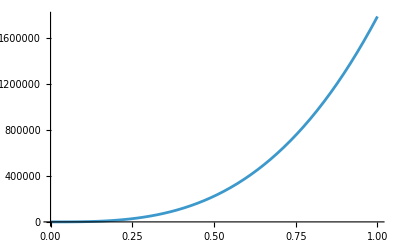

{{II→-0.0000332957-9.85214×10^-7 ⅈ},{II→-0.0000332957+9.85214×10^-7 ⅈ},{II→0.000131036},{II→6834.31}}

{{P[t]→ⅇ^(-mu t) (-1+ⅇ^(mu t)+P0)}}

```mathematica
testparams ={δp->0.001,γp->0.004,σ->0.125,α->365/3,β->600,μ->1/50}
Plot[(reduced[[1]]/. testparams),{II,0,1}]
Solve[(reduced[[1]]/. testparams)==0,II]
```